## APPM 5560 Homework 1

### Question 3

A uniform distribution PDF on [0,1] is defined as 1 for θ ∈ (0,1) and 0 otherwise.
The uniform distribution CDF on [0,1] is 0 for θ < 0, the line y = θ (where y is the probability of θ < θ_0) and 1 for θ > 1.
For pretty looking graphs, they will be plotted using Mathematica, as opposed to by hand.

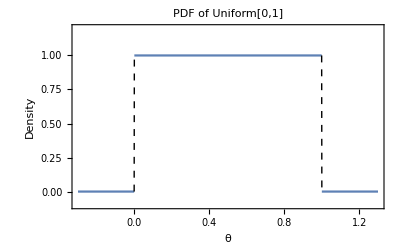

```mathematica
Plot[PDF[UniformDistribution[{0,1}],θ],{θ, -0.3,1.3},ExclusionsStyle->Dashed,PlotRange->{-0.1,1.2},PlotLabel->"PDF of Uniform[0,1]",Frame->True,FrameLabel->{"θ","Density"},Axes->{True,False}]
```

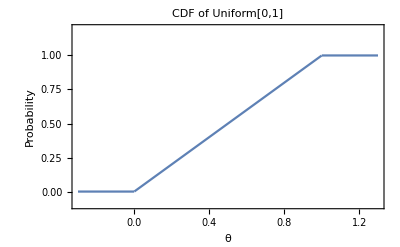

```mathematica
Plot[CDF[UniformDistribution[{0,1}],θ],{θ,-0.3,1.3},PlotRange->{-0.1,1.2},PlotLabel->"CDF of Uniform[0,1]",Frame->True,FrameLabel->{"θ", "Probability"},Axes->{True,False}]
```